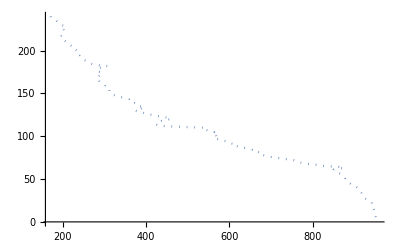

```mathematica
p=ListLinePlot[Import["/home/aaron/Developer/robotics/micromouse/plots/leftdiag.full","Table"],PlotStyle->Dotted]
```

```mathematica
Manipulate[Show[p,Plot[a*(x-b)^c+d,{x,50,1000}]],{a,-0.01,-0.0001},{b,700,900},{c,0.001,10},{d,-400,400}]
```